# Cross Ratio

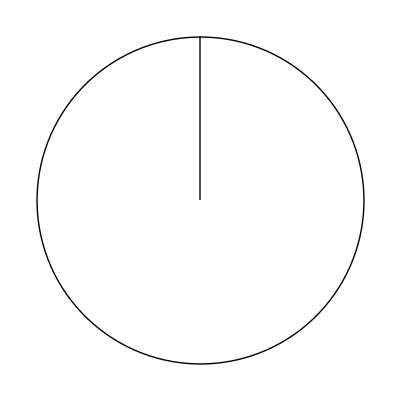

```mathematica
Graphics[{Circle[],Line[{{0,0},{0,1}}]}]
```

```mathematica
CrossRatio[a_,b_,c_,d_]:=a/b/(c/d)
```

```mathematica
CrossRatio[1,2,2,3]
```

3/4

```mathematica
Solve[CrossRatio[1,2,1+x,2+x]==1,x]
```

{{x→0}}

```mathematica
Manipulate[Graphics[{
Line[{{0,0.5},{a,0.5}}],
Line[{{a,0.3},{a-b,0.3}}],
Line[{{0,0.1},{c,0.1}}],
Line[{{a-b,-0.1},{c,-0.1}}]}],{a,1,3},{b,1,3},{c,1,3}]
```

```mathematica
Plot3D[CrossRatio[1,y,1+x,y+x],{x,-0.5,1},{y,-1,1}]
```